```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
ρ=1-1/10^9;
SIGMA={{1/ρ,ρ},{ρ,1/ρ}};U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
```

```mathematica
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
```

```mathematica
dU[x_,y_]=GradientG[U[x,y],{x,y}];
```

```mathematica
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

501 342.569 8.76351 0.710502 0.408969 5.68584 348.254 400.321 9.55594×10^-7 0.00662641 True {1,6,8,10,11} {1,11}

1002 388.303 6.3566 0.664913 0.325301 7.504 309.912 395.807 1.2719×10^-6 0.0142043 False {1,2,8,11} {1,8,11}

1503 330.429 5.2247 0.515491 0.419221 9.50336 339.933 395.807 1.15627×10^-6 0.0171872 True {1,11} {1,11}

2004 314.672 7.81367 0.551892 0.474314 11.1823 372.01 325.855 1.39908×10^-6 0.0207965 False {1,2,11} {1,11}

2505 272.583 8.69262 0.634146 0.343346 15.1592 287.742 244.118 1.15627×10^-6 0.0251638 True {1,2,4,11} {1,11}

3006 232.151 3.86039 0.461032 0.468669 11.9673 287.742 244.118 1.05115×10^-6 0.0304482 False {1,2,3,7,11} {1,2,3,11}

3507 338.488 14.0799 0.558495 0.393112 8.16186 346.65 244.118 1.05115×10^-6 0.0207965 True {1,3,5,7,11} {1,11}

4008 236.774 5.9464 0.319115 0.382867 7.34385 346.65 244.118 1.15627×10^-6 0.0276801 False {1,4,6,7} {1,11}

4509 312.791 16.6652 0.653204 0.353787 13.7581 326.549 244.118 9.55594×10^-7 0.0251638 True {1,4,6,7,11} {1,11}

5010 234.483 7.33914 0.643001 0.449277 9.63521 296.927 244.118 1.2719×10^-6 0.0251638 False {1,3,7,8,11} {1,11}

5511 286.215 10.9212 0.546453 0.442291 10.7122 296.927 244.118 1.2719×10^-6 0.0251638 True {1,2,7,11} {1,11}

6012 236.096 6.41533 0.378663 0.413095 8.02232 296.927 244.118 1.2719×10^-6 0.0251638 False {1,3,8,9} {1,11}

6513 289.897 12.5209 0.577643 0.381071 7.03028 296.927 244.118 1.2719×10^-6 0.0251638 True {1,2,4,9,11} {1,10,11}

7014 235.117 20.0497 0.752398 0.395539 9.00156 296.927 244.118 1.2719×10^-6 0.0251638 False {1,3,5,9,11} {1,11}

7515 289.769 5.90574 0.827527 0.265483 7.15829 296.927 244.118 1.2719×10^-6 0.0251638 True {1,2,5,6,8,11} {1,11}

8016 229.185 15.8992 0.686478 0.340634 14.9336 296.927 244.118 1.2719×10^-6 0.0251638 False {1,2,5,6,7,8,11} {1,5,11}

8517 275.911 8.94627 0.66347 0.386516 21.0162 296.927 244.118 1.2719×10^-6 0.0251638 True {1,4,11} {1,6,11}

9018 236.759 8.13658 0.398025 0.391069 7.35898 296.927 244.118 1.2719×10^-6 0.0251638 False {1,3,11} {1,11}

9519 291.18 7.45482 0.581363 0.348676 5.74671 296.927 244.118 1.2719×10^-6 0.0251638 True {1,3,4,5,11} {1,11}

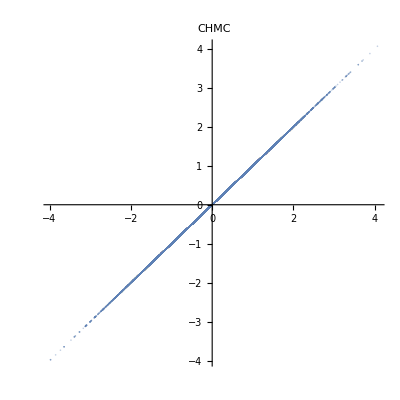

{0.975549,0.963245}

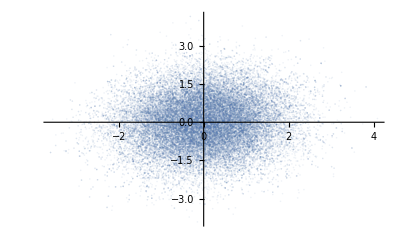

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True];
ListPlot[QS,PlotLabel->CHMC,PlotStyle->Opacity[.2],AspectRatio->1]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1,PlotStyle->Opacity[.1]]
```

501 401.637 7.26342 0.4218 0.422112 6.02955 407.667 2.43063×10^9 8.68722×10^-7 0.0001 True {1,3,7} {1,11}

1002 302.977 7.83749 0.537882 0.395855 5.82691 308.804 2.43063×10^9 1.15627×10^-6 0.0001 True {1,3,7,10,11} {1,11}

1503 265.352 11.4485 0.597374 0.431026 4.77539 270.127 2.43063×10^9 1.39908×10^-6 0.0001 True {1,2,6,11} {1,11}

2004 252.59 12.2225 0.548133 0.455365 4.72092 257.311 2.43063×10^9 1.2719×10^-6 0.0001 True {1,3,6,11} {1,11}

2505 331.121 8.66174 0.757732 0.334687 8.41997 339.541 2.43063×10^9 1.05115×10^-6 0.0001 True {1,5,6,11} {1,11}

3006 331.925 7.72373 0.623299 0.427718 6.8254 338.751 2.43063×10^9 1.15627×10^-6 0.0001 True {1,2,3,6,8,9,11} {1,11}

3507 251.932 7.97046 0.633129 0.407198 7.98541 259.918 2.43063×10^9 1.39908×10^-6 0.0001 True {1,4,11} {1,9,11}

4008 276.074 12.9335 0.438961 0.398441 6.10717 282.181 2.43063×10^9 1.15627×10^-6 0.0001 True {1,2,4,11} {1,11}

4509 277.035 7.77287 0.547215 0.368212 5.14654 282.181 2.43063×10^9 1.2719×10^-6 0.0001 True {1,2,5,6,11} {1,11}

5010 357.326 21.2724 0.687868 0.36285 6.03735 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,4,5,11} {1,11}

5511 352.864 7.78507 0.686434 0.406085 10.4999 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,2,7,9,10,11} {1,11}

6012 359.029 7.21309 0.549577 0.402206 4.33486 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,6,11} {1,11}

6513 355.126 10.6078 0.789186 0.279783 8.23792 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,4,5,7,9,11} {1,11}

7014 353.267 9.76882 0.545222 0.384376 10.0961 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,3,5,11} {1,11}

7515 355.011 7.825 0.48677 0.36471 8.35276 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,2,11} {1,11}

8016 355.324 12.0689 0.758004 0.362308 8.03937 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,11} {1,3,6,11}

8517 353.506 7.60714 0.66921 0.399542 9.85763 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,3,7,9,11} {1,11}

9018 353.192 14.2555 0.646048 0.422326 10.1714 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,2,4,7,9,11} {1,11}

9519 356.045 7.90029 0.586137 0.429283 7.31871 363.363 2.43063×10^9 1.15627×10^-6 0.0001 True {1,2,6,11} {1,11}

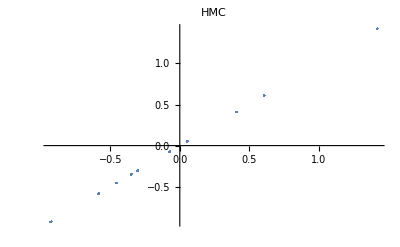

{0.843047,0.825736}

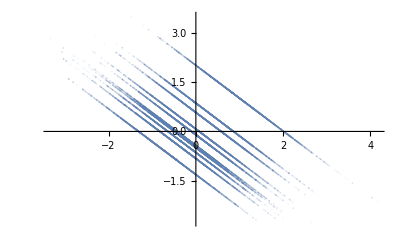

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False];
ListPlot[QS,PlotLabel->HMC,PlotStyle->Opacity[.1]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1,PlotStyle->Opacity[.1]]
```

501 1.06758×10^9 6.9227 0.1 0.316228 8.79587×10^7 2.3909×10^9 1.15553×10^9 1.×10^-9 0.00970172 False {1,2,3,11} {5,8,11}

1002 1.95372×10^8 3.78963 0.4 0.516398 2.8808×10^7 2.3909×10^9 2.2418×10^8 1.×10^-9 0.00547637 False {1,2,5,11} {1,11}

1503 1.01356×10^8 12.4759 0.4 0.516398 1.5768×10^7 2.3909×10^9 1.17124×10^8 1.×10^-9 0.00662641 False {1,2,5,6,11} {1,11}

2004 5.3027×10^7 9.12513 0.2 0.421637 5.55656×10^6 2.3909×10^9 5.85836×10^7 1.×10^-9 0.00728905 False {1,2,3,4,6,11} {1,11}

2505 2.44322×10^7 4.54198 0.2 0.421637 2.43032×10^6 2.3909×10^9 2.68625×10^7 1.×10^-9 0.00602401 False {1,5,11} {1,11}

3006 9.35835×10^6 10.7 0.2 0.421637 1.13498×10^6 2.3909×10^9 1.04933×10^7 1.×10^-9 0.00602401 False {1,3,7,10} {1,10,11}

3507 3.90912×10^6 8.40799 0.3 0.483046 594459. 2.3909×10^9 4.50358×10^6 1.×10^-9 0.00547637 False {1,2,3,11} {1,3,11}

4008 2.03199×10^6 14.4001 0.3 0.483046 248538. 2.3909×10^9 2.28053×10^6 1.×10^-9 0.00728905 False {1,3,4,11} {1,11}

4509 864322. 16.0618 0.2 0.421637 96991.3 2.3909×10^9 961314. 1.×10^-9 0.00728905 False {1,6,11} {1,11}

5010 478998. 8.77233 0.1 0.316228 49366.6 2.3909×10^9 528365. 1.×10^-9 0.00602401 False {1,2,3,4,5,11} {1,11}

5511 285825. 9.07383 0.2 0.421637 27553.4 2.3909×10^9 313379. 1.×10^-9 0.00662641 False {1,2,11} {1,11}

6012 108792. 10.1285 0.301963 0.481718 14159.3 2.3909×10^9 122951. 1.×10^-9 0.00662641 False {1,2,3,4,11} {1,5,11}

6513 47726.8 3.07087 0.0169976 0.0342118 5253.79 2.3909×10^9 52980.6 1.×10^-9 0.00881975 False {1,4} {10,11}

7014 18996.8 10.3471 0.235403 0.361667 1301.72 2.3909×10^9 20298.5 1.×10^-9 0.00602401 False {1,5,11} {1,11}

7515 14783.9 3.9587 0.502746 0.443732 715.707 2.3909×10^9 15499.6 1.×10^-9 0.00411448 False {1,2,3,4,8,11} {1,11}

8016 15018.9 10.6337 0.408945 0.388687 480.698 2.3909×10^9 15499.6 1.×10^-9 0.00374043 False {1,2,3,6,11} {1,11}

8517 13816.9 11.93 0.461799 0.423679 313.152 2.3909×10^9 14130.1 1.×10^-9 0.00340039 False {1,3,5,10,11} {1,11}

9018 13903.2 10.1926 0.570094 0.397357 226.859 2.3909×10^9 14130.1 1.×10^-9 0.00309127 False {1,3,4,5,8,11} {1,11}

9519 13958.8 11.2558 0.379164 0.362444 171.305 2.3909×10^9 14130.1 1.×10^-9 0.00281024 False {1,2,4,11} {1,11}

10020 12536.9 8.02209 0.520662 0.359033 127.315 2.3909×10^9 12664.2 1.×10^-9 0.00281024 False {1,2,6,7,11} {1,11}

10521 8342.52 6.85937 0.524856 0.435227 88.1462 2.3909×10^9 8430.67 1.×10^-9 0.00411448 False {1,6,10,11} {1,11}

11022 5553.85 2.76005 0.520034 0.325466 58.9053 2.3909×10^9 5612.75 1.×10^-9 0.00547637 False {1,3,4,8} {1,11}

11523 2460.39 18.0481 0.706419 0.393562 26.8252 2.3909×10^9 2487.22 1.×10^-9 0.00728905 False {1,2,5,7,8,11} {1,11}

12024 309.422 22.1195 0.461504 0.343524 5.24526 2.3909×10^9 314.667 1.×10^-9 0.0171872 False {1,3,6,10} {1,11}

12525 77.3875 22.0024 0.449766 0.348035 2.15526 2.3909×10^9 79.5428 1.×10^-9 0.0405265 False {1,2,3,6,7} {1,11}

13026 92.201 7.14915 0.567356 0.346917 2.88569 2.3909×10^9 95.0867 1.×10^-9 0.0405265 False {1,3,4,5,11} {1,11}

13527 63.0421 6.80973 0.527121 0.458171 4.62609 2.3909×10^9 67.6682 1.×10^-9 0.0445792 False {1,2,11} {1,7,11}

14028 65.43 8.62394 0.612859 0.389102 2.23814 2.3909×10^9 67.6682 1.×10^-9 0.0490371 False {1,3,4,5,6,7,11} {1,11}

14529 64.4053 20.7882 0.412804 0.383872 2.50329 2.3909×10^9 66.9085 1.×10^-9 0.0445792 False {1,2,4,11} {1,11}

15030 67.6045 12.8012 0.662331 0.38813 5.60858 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,7,10,11} {1,11}

15531 71.9542 8.54968 0.553756 0.399024 1.25895 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,2,4,5,11} {1,2,11}

16032 67.6086 7.41017 0.559904 0.432744 5.60449 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,2,3,5,8,10,11} {1,11}

16533 69.1845 4.83851 0.590029 0.430999 4.02856 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,2,3,11} {1,6,11}

17034 68.4517 7.99776 0.608385 0.42385 4.76136 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,2,3,4,10,11} {1,11}

17535 64.5165 21.9824 0.395856 0.335484 8.69657 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,2,3,11} {1,10,11}

18036 66.1056 15.7516 0.499343 0.433526 7.10751 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,4,5,11} {1,2,9,11}

18537 70.2824 2.98816 0.597553 0.346521 2.93068 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,3,4,7,11} {1,11}

19038 69.2555 22.1881 0.604623 0.363374 3.9576 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,2,4,5,6,10,11} {1,11}

19539 69.9041 15.1383 0.576822 0.368573 3.30902 2.3909×10^9 73.2131 1.×10^-9 0.0445792 False {1,4,5,8,11} {1,11}

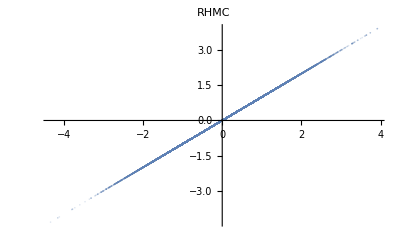

{0.680643,0.680643}

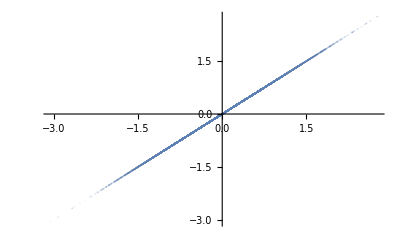

```mathematica
QS=hmc[U,dU,ddU,2,15000,20000,False,False];
ListPlot[QS,PlotLabel->RHMC,PlotStyle->Opacity[.2]]
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1,PlotStyle->Opacity[.1]]
```